# x-Y Phase Spaces and Potentials

## Set-up

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Define the energy density of dark matter (z) and the energy density of radiation (v) in terms of the energy density of dark energy (x)*)
z[x_,c_]=c*((x-R)/(1-x))^(1/(1-R));

v[x_,cv_]=cv*((x-R)/(1-x))^(4/(3*(1-R)));
```

```mathematica
(*Define compact Z and V variables to range between 0 and 1*)
Z[x_,c_]=Simplify[z[x,c]/(1+z[x,c])]
```

(c ((R-x)/(-1+x))^(1/(1-R)))/(1+c ((R-x)/(-1+x))^(1/(1-R)))

```mathematica
V[x_,cv_]=Simplify[v[x,cv]/(1+v[x,cv])]
```

(cv ((R-x)/(-1+x))^(4/(3-3 R)))/(1+cv ((R-x)/(-1+x))^(4/(3-3 R)))

## Find the Fixed Points of the System

```mathematica
(*System of dimensionless differential equations*)
(*Dark energy, x, compact Hubble expansion, Y, compact dark matter, Z, and compact radiation, V*)
de1:=x'=-3*(Y/(1-Y^2)^(1/2))*(x-R)*(1-x)
de2:=Y'=-Y^2*(1-Y^2)^(1/2)-(((1-Y^2)^(3/2))/6)*((Z/(1-Z))+2*V/(1-V)-3*R+x*(1+3*R)-3*x^2)
de3:=Z'=-3*Y*Z*(1-Z)/((1-Y^2)^(1/2))
de4:=V'=-4*Y*V*(1-V)/((1-Y^2)^(1/2))
```

```mathematica
(*Find the fixed points of the system*)
FPs=Solve[{de1==0,de2==0,de3==0,de4==0},{x,Y,Z,V}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Y→0,V→(-3 R+x+3 R x-3 x^2+Z+3 R Z-x Z-3 R x Z+3 x^2 Z)/(-2-3 R+x+3 R x-3 x^2+3 Z+3 R Z-x Z-3 R x Z+3 x^2 Z)},{Y→0,Z→0,V→(-3 R+x+3 R x-3 x^2)/(-2-3 R+x+3 R x-3 x^2)},{x→1,Y→0,V→(-2+3 Z)/(-4+5 Z)},{x→R,Y→0,V→(-2 R+Z+2 R Z)/(-2-2 R+3 Z+2 R Z)},{Y→0,Z→(-3 R+x+3 R x-3 x^2)/(-1-3 R+x+3 R x-3 x^2),V→0},{x→1,Y→-1/2,Z→0,V→0},{x→1,Y→1/2,Z→0,V→0},{x→R,Y→-(√R)/(√(3+R)),Z→0,V→0},{x→R,Y→(√R)/(√(3+R)),Z→0,V→0},{x→1/6 (1+3 R-√(1-30 R+9 R^2)),Y→0,Z→0,V→0},{x→1/6 (1+3 R+√(1-30 R+9 R^2)),Y→0,Z→0,V→0},{x→1,Y→0,Z→0,V→1/2},{x→R,Y→0,Z→0,V→R/(1+R)},{x→1,Y→0,Z→2/3,V→0},{x→R,Y→0,Z→(2 R)/(1+2 R),V→0}}

```mathematica
(*Remove arrows from fixed points*)
FP[1]={x,Y/.FPs[[1,1]],Z,V/.FPs[[1,2]]};
FP[2]={x,Y/.FPs[[2,1]],Z/.FPs[[2,2]],V/.FPs[[2,3]]};
FP[3]={x/.FPs[[3,1]],Y/.FPs[[3,2]],Z,V/.FPs[[3,3]]};
FP[4]={x/.FPs[[4,1]],Y/.FPs[[4,2]],Z,V/.FPs[[4,3]]};
FP[5]={x,Y/.FPs[[5,1]],Z/.FPs[[5,2]],V/.FPs[[5,3]]};
FP[6]={x/.FPs[[6,1]],Y/.FPs[[6,2]],Z/.FPs[[6,3]],V/.FPs[[6,4]]};
FP[7]={x/.FPs[[7,1]],Y/.FPs[[7,2]],Z/.FPs[[7,3]],V/.FPs[[7,4]]};
FP[8]={x/.FPs[[8,1]],Y/.FPs[[8,2]],Z/.FPs[[8,3]],V/.FPs[[8,4]]};
FP[9]={x/.FPs[[9,1]],Y/.FPs[[9,2]],Z/.FPs[[9,3]],V/.FPs[[9,4]]};
FP[10]={x/.FPs[[10,1]],Y/.FPs[[10,2]],Z/.FPs[[10,3]],V/.FPs[[10,4]]};
FP[11]={x/.FPs[[11,1]],Y/.FPs[[11,2]],Z/.FPs[[11,3]],V/.FPs[[11,4]]};
FP[12]={x/.FPs[[12,1]],Y/.FPs[[12,2]],Z/.FPs[[12,3]],V/.FPs[[12,4]]};
FP[13]={x/.FPs[[13,1]],Y/.FPs[[13,2]],Z/.FPs[[13,3]],V/.FPs[[13,4]]};
FP[14]={x/.FPs[[14,1]],Y/.FPs[[14,2]],Z/.FPs[[14,3]],V/.FPs[[14,4]]};
```

```mathematica
(*Define fixed points not found using Solve*)
(*These are the fixed points at Y = +/- 1*)
FP[15]={R,1,Z,V};
FP[16]={R,-1,Z,V};
FP[17]={1,1,Z,V};
FP[18]={1,-1,Z,V};
```

```mathematica
(*Put fixed points into one variable name*)
FPs=Table[FP[i],{i,1,18}];
```

```mathematica
(*4D Jacobian matrix for general system of equations. D[] differentiates each expression*)
J=Simplify[{{D[de1,x],D[de1,Y],D[de1,Z],D[de1,V]}, {D[de2,x],D[de2,Y],D[de2,Z],D[de2,V]},{D[de3,x],D[de3,Y],D[de3,Z],D[de3,V]},{D[de4,x],D[de4,Y],D[de4,Z],D[de4,V]}}];
J//MatrixForm
```

(-(3 (1+R-2 x) Y)/(√(1-Y^2)) | (3 (-1+x) (-R+x))/((1-Y^2)^(3/2)) | 0 | 0
-1/6 (1+3 R-6 x) (1-Y^2)^(3/2) | (Y (2 Y^2+4 (-1+Y^2)+(1-Y^2) (-(2 V)/(-1+V)+3 R (-1+x)+x-3 x^2+Z/(1-Z))))/(2 √(1-Y^2)) | -((1-Y^2)^(3/2))/(6 (-1+Z)^2) | -((1-Y^2)^(3/2))/(3 (-1+V)^2)
0 | (3 (-1+Z) Z)/((1-Y^2)^(3/2)) | (3 Y (-1+2 Z))/(√(1-Y^2)) | 0
0 | (4 (-1+V) V)/((1-Y^2)^(3/2)) | 0 | (4 (-1+2 V) Y)/(√(1-Y^2)))

```mathematica
(*Find the Jacobian and eigenvalues for each fixed point*)
TableForm[Table[{FPs[[i]]//MatrixForm,Simplify[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->FPs[[i,1]],Y->FPs[[i,2]],Z->FPs[[i,3]],V->FPs[[i,4]]}]]//MatrixForm},{i,1,18}],TableHeadings->{None,{"Fixed Point", "Jacobian","Eigenvalues"}}]
```

Power::infy: Infinite expression 1/(√0) encountered.

Power::infy: Infinite expression 1/0^(3/2) encountered.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

Eigenvalues::inf: Input matrix contains an infinite entry.

Infinity::indet: Indeterminate expression 0 (-1+R) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Eigenvalues::inf: Input matrix contains an infinite entry.

General::stop: Further output of Eigenvalues::inf will be suppressed during this calculation.

Fixed Point | Jacobian | Eigenvalues
(x
0
Z
(-3 R+x+3 R x-3 x^2+Z+3 R Z-x Z-3 R x Z+3 x^2 Z)/(-2-3 R+x+3 R x-3 x^2+3 Z+3 R Z-x Z-3 R x Z+3 x^2 Z)) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/(6 (-1+Z)^2) | -((2+3 R (-1+x) (-1+Z)+x (-1+Z)-3 x^2 (-1+Z)-3 Z)^2)/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | (8 (3 R (-1+x) (-1+Z)+x (-1+Z)-3 x^2 (-1+Z)-Z) (-1+Z))/((2+3 R (-1+x) (-1+Z)+x (-1+Z)-3 x^2 (-1+Z)-3 Z)^2) | 0 | 0) | (0
0
-(√(x+9 R^2 (-1+x) (-1+Z)-9 x^2 (-1+Z)+18 x^3 (-1+Z)-9 R (-1-2 x+3 x^2) (-1+Z)+Z-x Z))/(√6 √(-1+Z))
(√(x+9 R^2 (-1+x) (-1+Z)-9 x^2 (-1+Z)+18 x^3 (-1+Z)-9 R (-1-2 x+3 x^2) (-1+Z)+Z-x Z))/(√6 √(-1+Z)))
(x
0
0
(-3 R+x+3 R x-3 x^2)/(-2-3 R+x+3 R x-3 x^2)) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/6 | -1/12 (-2+3 R (-1+x)+x-3 x^2)^2
0 | 0 | 0 | 0
0 | (8 (3 R (-1+x)+x-3 x^2))/((-2+3 R (-1+x)+x-3 x^2)^2) | 0 | 0) | (0
0
-(√(9 R^2 (-1+x)+R (9+18 x-27 x^2)+x (-1-9 x+18 x^2)))/(√6)
(√(9 R^2 (-1+x)+R (9+18 x-27 x^2)+x (-1-9 x+18 x^2)))/(√6))
(1
0
Z
(-2+3 Z)/(-4+5 Z)) | (0 | 0 | 0 | 0
1/6 (5-3 R) | 0 | -1/(6 (-1+Z)^2) | -(4-5 Z)^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (-2+3 Z))/(4-5 Z)^2 | 0 | 0) | (0
0
-(√(-8+9 Z))/(√6 √(-1+Z))
(√(-8+9 Z))/(√6 √(-1+Z)))
(R
0
Z
(-2 R+Z+2 R Z)/(-2-2 R+3 Z+2 R Z)) | (0 | 0 | 0 | 0
1/6 (-1+3 R) | 0 | -1/(6 (-1+Z)^2) | -(-2+2 R (-1+Z)+3 Z)^2/(12 (-1+Z)^2)
0 | 3 (-1+Z) Z | 0 | 0
0 | -(8 (-1+Z) (2 R (-1+Z)+Z))/(-2+2 R (-1+Z)+3 Z)^2 | 0 | 0) | (0
0
-(√(8 R (-1+Z)+Z))/(√6 √(-1+Z))
(√(8 R (-1+Z)+Z))/(√6 √(-1+Z)))
(x
0
(-3 R+x+3 R x-3 x^2)/(-1-3 R+x+3 R x-3 x^2)
0) | (0 | 3 (-1+x) (-R+x) | 0 | 0
-1/6-R/2+x | 0 | -1/6 (-1+3 R (-1+x)+x-3 x^2)^2 | -1/3
0 | (3 (3 R (-1+x)+x-3 x^2))/((-1+3 R (-1+x)+x-3 x^2)^2) | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(3 R^2 (-1+x)+2 x^2 (-2+3 x)+R (2+7 x-9 x^2)))/(√2)
(√(3 R^2 (-1+x)+2 x^2 (-2+3 x)+R (2+7 x-9 x^2)))/(√2))
(1
-1/2
0
0) | (√3 (-1+R) | 0 | 0 | 0
1/16 √3 (5-3 R) | 2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | √3 | 0
0 | 0 | 0 | 4/(√3)) | (4/(√3)
√3
2/(√3)
√3 (-1+R))
(1
1/2
0
0) | (-√3 (-1+R) | 0 | 0 | 0
1/16 √3 (5-3 R) | -2/(√3) | -(√3)/16 | -(√3)/8
0 | 0 | -√3 | 0
0 | 0 | 0 | -4/(√3)) | (-4/(√3)
-√3
-2/(√3)
-√3 (-1+R))
(R
-(√R)/(√(3+R))
0
0) | (-√3 (-1+R) √R √(1/(3+R)) √(3+R) | 0 | 0 | 0
1/2 √3 (1/(3+R))^(3/2) (-1+3 R) | (2 √R √(1/(3+R)) √(3+R))/(√3) | -1/2 √3 (1/(3+R))^(3/2) | -√3 (1/(3+R))^(3/2)
0 | 0 | √3 √R √(1/(3+R)) √(3+R) | 0
0 | 0 | 0 | (4 √R √(1/(3+R)) √(3+R))/(√3)) | ((2 √R √(1/(3+R)) √(3+R))/(√3)
√3 √R √(1/(3+R)) √(3+R)
(4 √R √(1/(3+R)) √(3+R))/(√3)
-√3 (-1+R) √R √(1/(3+R)) √(3+R))
(R
(√R)/(√(3+R))
0
0) | (√3 (-1+R) √R √(1/(3+R)) √(3+R) | 0 | 0 | 0
1/2 √3 (1/(3+R))^(3/2) (-1+3 R) | -(2 √R √(1/(3+R)) √(3+R))/(√3) | -1/2 √3 (1/(3+R))^(3/2) | -√3 (1/(3+R))^(3/2)
0 | 0 | -√3 √R √(1/(3+R)) √(3+R) | 0
0 | 0 | 0 | -(4 √R √(1/(3+R)) √(3+R))/(√3)) | (-(4 √R √(1/(3+R)) √(3+R))/(√3)
-√3 √R √(1/(3+R)) √(3+R)
-(2 √R √(1/(3+R)) √(3+R))/(√3)
√3 (-1+R) √R √(1/(3+R)) √(3+R))
(1/6 (1+3 R-√(1-30 R+9 R^2))
0
0
0) | (0 | 1/3 (-1-3 R+√(1-30 R+9 R^2)) | 0 | 0
-1/6 √(1-30 R+9 R^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1-9 R^2+√(1-30 R+9 R^2)+3 R (10+√(1-30 R+9 R^2))))/(3 √2)
(√(-1-9 R^2+√(1-30 R+9 R^2)+3 R (10+√(1-30 R+9 R^2))))/(3 √2))
(1/6 (1+3 R+√(1-30 R+9 R^2))
0
0
0) | (0 | 1/3 (-1-3 R-√(1-30 R+9 R^2)) | 0 | 0
1/6 √(1-30 R+9 R^2) | 0 | -1/6 | -1/3
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0
0
-(√(-1-9 R^2-√(1-30 R+9 R^2)-3 R (-10+√(1-30 R+9 R^2))))/(3 √2)
(√(-1-9 R^2-√(1-30 R+9 R^2)-3 R (-10+√(1-30 R+9 R^2))))/(3 √2))
(1
0
0
1/2) | (0 | 0 | 0 | 0
1/6 (5-3 R) | 0 | -1/6 | -4/3
0 | 0 | 0 | 0
0 | -1 | 0 | 0) | (-2/(√3)
2/(√3)
0
0)
(R
0
0
R/(1+R)) | (0 | 0 | 0 | 0
1/6 (-1+3 R) | 0 | -1/6 | -1/3 (1+R)^2
0 | 0 | 0 | 0
0 | -(4 R)/(1+R)^2 | 0 | 0) | (0
0
-(2 √R)/(√3)
(2 √R)/(√3))
(1
0
2/3
0) | (0 | 0 | 0 | 0
1/6 (5-3 R) | 0 | -3/2 | -1/3
0 | -2/3 | 0 | 0
0 | 0 | 0 | 0) | (-1
1
0
0)
(R
1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]
(R
-1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]
(1
1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]
(1
-1
Z
V) | (ComplexInfinity | Indeterminate | 0 | 0
0 | ComplexInfinity | 0 | 0
0 | ComplexInfinity | ComplexInfinity | 0
0 | ComplexInfinity | 0 | ComplexInfinity) | Eigenvalues[{{ComplexInfinity,Indeterminate,0,0},{0,ComplexInfinity,0,0},{0,ComplexInfinity,ComplexInfinity,0},{0,ComplexInfinity,0,ComplexInfinity}}]

## Find c for the Limiting Cases with 2 Einstein Points

```mathematica
(*Define w, the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
w[x_,c_,cv_]=z[x,c]+2*v[x,cv]-3*R+x*(1+3*R)-3*x^2
```

-3 R+(1+3 R) x-3 x^2+c ((-R+x)/(1-x))^(1/(1-R))+2 cv ((-R+x)/(1-x))^(4/(3 (1-R)))

```mathematica
(*Define compact W*)
W[x_,c_,cv_]=w[x,c,cv]/Sqrt[1+w[x,c,cv]^2]
```

(-3 R+(1+3 R) x-3 x^2+c ((-R+x)/(1-x))^(1/(1-R))+2 cv ((-R+x)/(1-x))^(4/(3 (1-R))))/(√(1+(-3 R+(1+3 R) x-3 x^2+c ((-R+x)/(1-x))^(1/(1-R))+2 cv ((-R+x)/(1-x))^(4/(3 (1-R))))^2))

```mathematica
(*Find the limit of w when x -> 1*)
Limit[w[x,c,cv],x->1, Assumptions->{c>0,cv>0,0<R<1}]
```

∞

```mathematica
(*Find the limit of w when x -> 0*)
(*Here, R -> 0 too as R < x < 1*)
Limit[w[x,c,cv],x->0, Assumptions->{c>0,cv>0,0<R<1}]
```

ConditionalExpression[2 cv (-R)^(4/(3-3 R))+c (-R)^(1/(1-R))-3 R, 1/(1-R)∈ℤ&&4/(3-3 R)∈ℤ]

```mathematica
(*Findthe limit of w when x -> R*)
(*The limit is negative when x -> R and positive when x -> 1, meaning there is always at least 1 Einstein point as w must cross the x-axis at least once for R < x < 1*)
Limit[w[x,c,cv],x->R,Assumptions->{c>0,cv>0,0<R<1}]
```

-2 R

```mathematica
(*First derivative of w with respect to x*)
wDeriv[x_,c_,cv_]=Simplify[D[w[x,c,cv],x]]
```

(8 cv ((R-x)/(-1+x))^(4/(3-3 R))+3 c ((R-x)/(-1+x))^(1/(1-R))+9 R^2 (-1+x)+3 x-21 x^2+18 x^3-3 R (1-10 x+9 x^2))/(3 (R-x) (-1+x))

```mathematica
(*Rearrange dw/dx = 0 for c*)
xsol[c_]=Solve[wDeriv[x,c,cv]==0,c];
```

```mathematica
(*Remove arrow from solution above*)
c=c/.xsol[c]
```

{(R-x) ((R-x)/(-1+x))^(-1/(1-R)) (-1+x) (-(3 R^2)/(R-x)-(8 cv ((R-x)/(-1+x))^(4/(3-3 R)))/(3 (R-x) (-1+x))-x/((R-x) (-1+x))+(7 x^2)/((R-x) (-1+x))-(6 x^3)/((R-x) (-1+x))+(R (1-10 x+9 x^2))/((R-x) (-1+x)))}

```mathematica
(*w with cv found above substituted in*)
w[x,c,cv]
```

{-3 R+(1+3 R) x-3 x^2+2 cv ((-R+x)/(1-x))^(4/(3 (1-R)))+(R-x) ((R-x)/(-1+x))^(-1/(1-R)) (-1+x) ((-R+x)/(1-x))^(1/(1-R)) (-(3 R^2)/(R-x)-(8 cv ((R-x)/(-1+x))^(4/(3-3 R)))/(3 (R-x) (-1+x))-x/((R-x) (-1+x))+(7 x^2)/((R-x) (-1+x))-(6 x^3)/((R-x) (-1+x))+(R (1-10 x+9 x^2))/((R-x) (-1+x)))}

```mathematica
(*Define R and cv*)
(*The value for R was chosen as it shows all possible dynamical behaviour, and cv is calculated from the density parameters*)
R=0.05;
cv=0.000034;
```

```mathematica
(*w with R, c and cv found above substituted in*)
w[x,c,cv]
```

{-0.15+0.000068 ((-0.05+x)/(1-x))^1.40351+1.15 x-3 x^2+((0.05-x) (-1+x) ((-0.05+x)/(1-x))^1.05263 (-0.0075/(0.05-x)-(0.0000906667 ((0.05-x)/(-1+x))^1.40351)/((0.05-x) (-1+x))-x/((0.05-x) (-1+x))+(7 x^2)/((0.05-x) (-1+x))-(6 x^3)/((0.05-x) (-1+x))+(0.05 (1-10 x+9 x^2))/((0.05-x) (-1+x))))/((0.05-x)/(-1+x))^1.05263}

```mathematica
(*Numerically solve w with c found above for x*)
(*FindRoot is a Newtonian approximation*)
x1=FindRoot[w[x,c,cv]==0,{x,0.1}];
x2=FindRoot[w[x,c,cv]==0,{x,0.6}];
```

```mathematica
(*Remove arrows from solutions above*)
x1=x/.x1
x2=x/.x2
```

0.246638

0.599307

```mathematica
(*Clear the value of c*)
Clear[c];
```

```mathematica
(*Find the values of c for x values found above*)
(*These values of c are the limiting cases where the system admits two Einstein points*)
(*Flatten removes the extra {} from the output*)
cLimitingCase1=Flatten[Solve[w[x1,c,cv]==0,c]]
```

{c→0.200851}

```mathematica
cLimitingCase2=Flatten[Solve[w[x2,c,cv]==0,c]]
```

{c→0.386125}

```mathematica
(*Remove arrows from solutions above*)
cLimitingCase1=c/.cLimitingCase1
cLimitingCase2=c/.cLimitingCase2
```

0.200851

0.386125

## Find c for the Limiting Case when there are 3 Einstein Points

```mathematica
(*To find the value of c in the limiting case where there are 3 Einstein points*)
```

```mathematica
(*Give an estimate of c in this case*)
cThreeEinsteinPointsLim=0.31951738471255725;
```

```mathematica
(*Find the Einstein points*)
ThreeEinsteinPointsc4i=FindRoot[w[x,cThreeEinsteinPointsLim,cv]==0,{x,0.1}]
ThreeEinsteinPointsc4ii=FindRoot[w[x,cThreeEinsteinPointsLim,cv]==0,{x,0.4}]
ThreeEinsteinPointsc4iii=FindRoot[w[x,cThreeEinsteinPointsLim,cv]==0,{x,0.9}]
```

{x→0.16904}

{x→0.42644}

{x→0.763046}

```mathematica
(*Remove arrows from solutions above*)
ThreeEinsteinPointsc4={x/.ThreeEinsteinPointsc4i,x/.ThreeEinsteinPointsc4ii,x/.ThreeEinsteinPointsc4iii}
```

{0.16904,0.42644,0.763046}

```mathematica
(*In this limiting case, the two Closed Friedmann Separatrix (CFS) curves are the same*)
(*Calculate c by equating the two CFS curves and check if the value returned is the same as the guess*)
(*This is an iterative process*)
cLimIter=Flatten[Solve[(ThreeEinsteinPointsc4[[1]]+z[ThreeEinsteinPointsc4[[1]],c]+v[ThreeEinsteinPointsc4[[1]],cv])*((1-ThreeEinsteinPointsc4[[1]])/(ThreeEinsteinPointsc4[[1]]-R))^(2/(3*(1-R)))==(ThreeEinsteinPointsc4[[3]]+z[ThreeEinsteinPointsc4[[3]],c]+v[ThreeEinsteinPointsc4[[3]],cv])*((1-ThreeEinsteinPointsc4[[3]])/(ThreeEinsteinPointsc4[[3]]-R))^(2/(3*(1-R))),c]]
```

{c→0.319517}

```mathematica
(*Remove arrow from solution above*)
cLimIter=c/.cLimIter
```

0.319517

```mathematica
(*The difference of the guess of c and the calculation of c from the CFS curve for the limiting case when*)
cLimIter-cThreeEinsteinPointsLim
```

2.37865×10^-13

## Plots to Show the Number of Einstein Points in Each Case

```mathematica
(*Defining values of c to show the full range of dynamical behaviour*)
(*There are 7 cases in total to consider*)
c={0.05,cLimitingCase1,0.25,cThreeEinsteinPointsLim,0.35,cLimitingCase2,0.5}
```

{0.05,0.200851,0.25,0.319517,0.35,0.386125,0.5}

```mathematica
(*Export the values of c found here to use in other notebooks*)
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\cValues.csv",c]*)
```

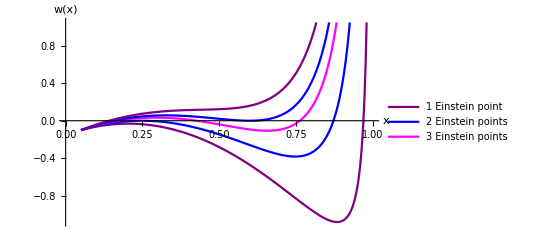

```mathematica
(*Plot w vs x for certain c values*)
(*Where w = 0 is where Einstein points exist*)
wplot=Plot[{w[x,c[[1]],cv],w[x,c[[2]],cv],w[x,c[[4]],cv],w[x,c[[6]],cv],w[x,c[[7]],cv]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points"},PlotStyle->{Purple,Blue, Magenta,Blue,Purple},AxesLabel->{"x","w(x)"}]
```

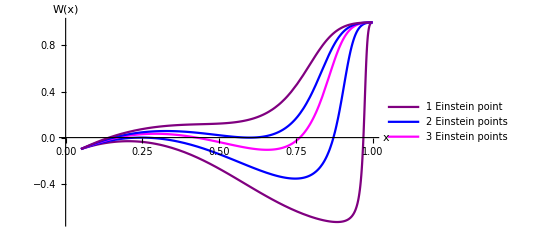

```mathematica
(*Plot compact W for certain c values*)
Wplot=Plot[{W[x,c[[1]],cv],W[x,c[[2]],cv],W[x,c[[4]],cv],W[x,c[[6]],cv],W[x,c[[7]],cv]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points"},PlotStyle->{Purple,Blue, Magenta,Blue,Purple},AxesLabel->{"x","W(x)"},ImageSize->{400,400}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\Wplot.pdf",Wplot]*)
```

```mathematica
(*Define zEinstein as w = 0 rearranged for z*)
zEinstein[x_]=3*R-(1+3*R)*x+3*x^2-2*v[x,cv];
```

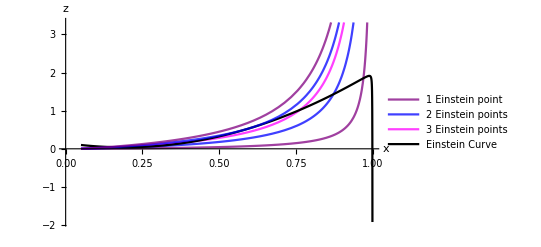

```mathematica
(*Plot of z(x) against the curves that show the number of Einstein points*)
zvsx=Plot[{z[x,c][[1]],z[x,c][[2]],z[x,c][[4]],zEinstein[x],z[x,c][[6]],z[x,c][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","Einstein Curve"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","z"}]
```

```mathematica
(*Define w(x) = 0 rearranged for v*)
vEinstein[x_]=0.5*(3*R-(1+3*R)*x+3*x^2-z[x,c]);
```

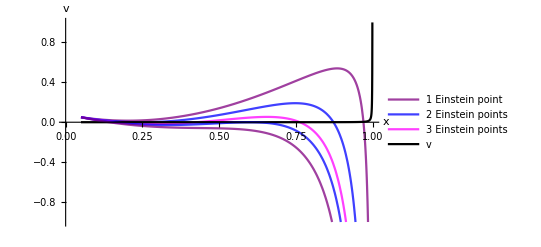

```mathematica
(*Plot of v(x) against the curves that show the number of Einstein points*)
vvsx=Plot[{vEinstein[x][[1]],vEinstein[x][[2]],vEinstein[x][[4]],v[x,cv],vEinstein[x][[6]],vEinstein[x][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","v"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","v"}, PlotRange->{-1,1}]
```

```mathematica
(*Define compact vEinstein[x]*)
VEinstein[x_]=vEinstein[x]/Sqrt[(1+vEinstein[x]^2)];
```

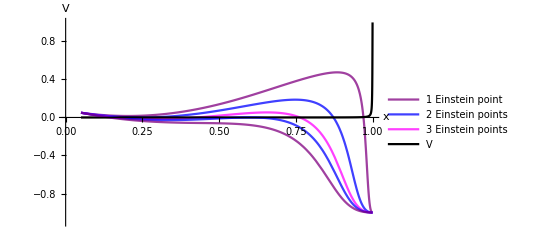

```mathematica
(*Plot of compact V(x) against the curves that show the number of Einstein points*)
Vvsx=Plot[{VEinstein[x][[1]],VEinstein[x][[2]],VEinstein[x][[4]],V[x,cv],VEinstein[x][[6]],VEinstein[x][[7]]},{x,0,1},PlotLegends->{"1 Einstein point","2 Einstein points", "3 Einstein points","V"},PlotStyle->{{Purple,Opacity[0.75]}, {Blue,Opacity[0.75]}, {Magenta,Opacity[0.75]},Black,{Blue,,Opacity[0.75]},{Purple,Opacity[0.75]}},AxesLabel->{"x","V"}, PlotRange->{-1.1,1}]
```

## Calculate the Einstein Points

```mathematica
(*Numerically solve w(x) = 0 to find the x values of the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
xOneEinsteinPointc1=FindRoot[w[x,c[[1]],cv]==0,{x,0.9}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc1=x/.xOneEinsteinPointc1
```

0.970205

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc1=Z[xOneEinsteinPointc1,c[[1]]]
```

0.649095

```mathematica
(*Calculate the V value of the Einstein point*)
VOneEinsteinPointc1=V[xOneEinsteinPointc1,cv]
```

0.00417376

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[1]={xOneEinsteinPointc1,0,ZOneEinsteinPointc1,VOneEinsteinPointc1}
```

{0.970205,0,0.649095,0.00417376}

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
xTwoEinsteinPointsc2i=FindRoot[w[x,c[[2]],cv]==0,{x,0.1}];
xTwoEinsteinPointsc2ii=FindRoot[w[x,c[[2]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc2={x/.xTwoEinsteinPointsc2i,x/.xTwoEinsteinPointsc2ii}
```

{0.246638,0.872521}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc2=Z[xTwoEinsteinPointsc2,c[[2]]]
```

{0.046572,0.588401}

```mathematica
(*Calculate the V values of the Einstein points*)
VTwoEinsteinPointsc2=V[xTwoEinsteinPointsc2,cv]
```

{5.1613×10^-6,0.000465273}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[2]={xTwoEinsteinPointsc2[[1]],0,ZTwoEinsteinPointsc2[[1]],VTwoEinsteinPointsc2[[1]]}
EinsteinFP[3]={xTwoEinsteinPointsc2[[2]],0,ZTwoEinsteinPointsc2[[2]],VTwoEinsteinPointsc2[[2]]}
```

{0.246638,0,0.046572,5.1613×10^-6}

{0.872521,0,0.588401,0.000465273}

### Three Einstein Points: c3

```mathematica
xThreeEinsteinPointsc3i=FindRoot[w[x,c[[3]],cv]==0,{x,0.1}];
xThreeEinsteinPointsc3ii=FindRoot[w[x,c[[3]],cv]==0,{x,0.4}];
xThreeEinsteinPointsc3iii=FindRoot[w[x,c[[3]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc3={x/.xThreeEinsteinPointsc3i,x/.xThreeEinsteinPointsc3ii,x/.xThreeEinsteinPointsc3iii}
```

{0.191121,0.338268,0.833281}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc3=Z[xThreeEinsteinPointsc3,c[[3]]]
```

{0.0382643,0.0944047,0.560286}

```mathematica
(*Calculate the V values of the Einstein points*)
VThreeEinsteinPointsc3=V[xThreeEinsteinPointsc3,cv]
```

{2.9323×10^-6,0.0000105917,0.000298136}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[4]={xThreeEinsteinPointsc3[[1]],0,ZThreeEinsteinPointsc3[[1]],VThreeEinsteinPointsc3[[1]]}
EinsteinFP[5]={xThreeEinsteinPointsc3[[2]],0,ZThreeEinsteinPointsc3[[2]],VThreeEinsteinPointsc3[[2]]}
EinsteinFP[6]={xThreeEinsteinPointsc3[[3]],0,ZThreeEinsteinPointsc3[[3]],VThreeEinsteinPointsc3[[3]]}
```

{0.191121,0,0.0382643,2.9323×10^-6}

{0.338268,0,0.0944047,0.0000105917}

{0.833281,0,0.560286,0.000298136}

### Three Einstein Points: c4

```mathematica
xThreeEinsteinPointsc4i=FindRoot[w[x,c[[4]],cv]==0,{x,0.1}];
xThreeEinsteinPointsc4ii=FindRoot[w[x,c[[4]],cv]==0,{x,0.4}];
xThreeEinsteinPointsc4iii=FindRoot[w[x,c[[4]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc4={x/.xThreeEinsteinPointsc4i,x/.xThreeEinsteinPointsc4ii,x/.xThreeEinsteinPointsc4iii}
```

{0.16904,0.42644,0.763046}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc4=Z[xThreeEinsteinPointsc4,c[[4]]]
```

{0.0396833,0.1702,0.50468}

```mathematica
(*Calculate the V values of the Einstein points*)
VThreeEinsteinPointsc4=V[xThreeEinsteinPointsc4,cv]
```

{2.2237×10^-6,0.0000188275,0.00015956}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[7]={xThreeEinsteinPointsc4[[1]],0,ZThreeEinsteinPointsc4[[1]],VThreeEinsteinPointsc4[[1]]}
EinsteinFP[8]={xThreeEinsteinPointsc4[[2]],0,ZThreeEinsteinPointsc4[[2]],VThreeEinsteinPointsc4[[2]]}
EinsteinFP[9]={xThreeEinsteinPointsc4[[3]],0,ZThreeEinsteinPointsc4[[3]],VThreeEinsteinPointsc4[[3]]}
```

{0.16904,0,0.0396833,2.2237×10^-6}

{0.42644,0,0.1702,0.0000188275}

{0.763046,0,0.50468,0.00015956}

### Three Einstein Points: c5

```mathematica
xThreeEinsteinPointsc5i=FindRoot[w[x,c[[5]],cv]==0,{x,0.1}];
xThreeEinsteinPointsc5ii=FindRoot[w[x,c[[5]],cv]==0,{x,0.4}];
xThreeEinsteinPointsc5iii=FindRoot[w[x,c[[5]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xThreeEinsteinPointsc5={x/.xThreeEinsteinPointsc5i,x/.xThreeEinsteinPointsc5ii,x/.xThreeEinsteinPointsc5iii}
```

{0.162562,0.474155,0.720075}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZThreeEinsteinPointsc5=Z[xThreeEinsteinPointsc5,c[[5]]]
```

{0.0406099,0.218225,0.467294}

```mathematica
(*Calculate the V values of the Einstein points*)
VThreeEinsteinPointsc5=V[xThreeEinsteinPointsc5,cv]
```

{2.03346×10^-6,0.0000251463,0.000115738}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[10]={xThreeEinsteinPointsc5[[1]],0,ZThreeEinsteinPointsc5[[1]],VThreeEinsteinPointsc5[[1]]}
EinsteinFP[11]={xThreeEinsteinPointsc5[[2]],0,ZThreeEinsteinPointsc5[[2]],VThreeEinsteinPointsc5[[2]]}
EinsteinFP[12]={xThreeEinsteinPointsc5[[3]],0,ZThreeEinsteinPointsc5[[3]],VThreeEinsteinPointsc5[[3]]}
```

{0.162562,0,0.0406099,2.03346×10^-6}

{0.474155,0,0.218225,0.0000251463}

{0.720075,0,0.467294,0.000115738}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
xTwoEinsteinPointsc6i=FindRoot[w[x,c[[6]],cv]==0,{x,0.1}];
xTwoEinsteinPointsc6ii=FindRoot[w[x,c[[6]],cv]==0,{x,0.9}];
```

```mathematica
(*Put the x values of the Einstein points into one variable name for this case*)
xTwoEinsteinPointsc6={x/.xTwoEinsteinPointsc6i,x/.xTwoEinsteinPointsc6ii}
```

{0.156181,0.599307}

```mathematica
(*Calculate the Z values of the Einstein points*)
ZTwoEinsteinPointsc6=Z[xTwoEinsteinPointsc6,c[[6]]]
```

{0.041747,0.349888}

```mathematica
(*Calculate the V values of the Einstein points*)
VTwoEinsteinPointsc6=V[xTwoEinsteinPointsc6,cv]
```

{1.85368×10^-6,0.0000529347}

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFP[13]={xTwoEinsteinPointsc6[[1]],0,ZTwoEinsteinPointsc6[[1]],VTwoEinsteinPointsc6[[1]]}
EinsteinFP[14]={xTwoEinsteinPointsc6[[2]],0,ZTwoEinsteinPointsc6[[2]],VTwoEinsteinPointsc6[[2]]}
```

{0.156181,0,0.041747,1.85368×10^-6}

{0.599307,0,0.349888,0.0000529347}

### One Einstein Point: c7

```mathematica
xOneEinsteinPointc7=FindRoot[w[x,c[[7]],cv]==0,{x,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
xOneEinsteinPointc7=x/.xOneEinsteinPointc7
```

0.141469

```mathematica
(*Calculate the Z value of the Einstein point*)
ZOneEinsteinPointc7=Z[xOneEinsteinPointc7,c[[7]]]
```

0.0452077

```mathematica
(*Calculate the V value of the Einstein point*)
VOneEinsteinPointc7=V[xOneEinsteinPointc7,cv]
```

1.46754×10^-6

```mathematica
(*Put the Einstein point into one variable name*)
EinsteinFP[15]={xOneEinsteinPointc7,0,ZOneEinsteinPointc7,VOneEinsteinPointc7}
```

{0.141469,0,0.0452077,1.46754×10^-6}

```mathematica
(*Find the eigenvalues of the Einstein fixed points*)
```

```mathematica
(*Put the Einstein points into one variable name*)
EinsteinFPs=Table[EinsteinFP[i],{i,1,15}];
```

```mathematica
(*Find the Jacobian and eigenvalues for each Einstein fixed point*)
TableForm[Table[{EinsteinFPs[[i]]//MatrixForm,Simplify[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],V->EinsteinFPs[[i,4]]}]//MatrixForm,Simplify[Eigenvalues[J/.{x->EinsteinFPs[[i,1]],Y->EinsteinFPs[[i,2]],Z->EinsteinFPs[[i,3]],V->EinsteinFPs[[i,4]]}]]//MatrixForm},{i,1,15}],TableHeadings->{{"c1","c2","","c3","","","c4","","","c5","","","c6","","c7"},{"Einstein Fixed Point", "Jacobian","Eigenvalues"}}]
```

| Einstein Fixed Point | Jacobian | Eigenvalues
c1 | (0.970205
0
0.649095
0.00417376) | (0. | -0.0822525 | 0 | 0
0.778538 | 0. | -1.35354 | -0.336133
0 | -0.683312 | 0. | 0
0 | -0.0166254 | 0 | 0.) | (-0.930827
0.930827
-4.97272×10^-17
0.)
c2 | (0.246638
0
0.046572
5.1613×10^-6) | (0. | -0.444419 | 0 | 0
0.0549714 | 0. | -0.183347 | -0.333337
0 | -0.133209 | 0. | 0
0 | -0.0000206451 | 0 | 0.) | (0.0000558519
-0.0000558516
-2.28035×10^-10
0.)
 | (0.872521
0
0.588401
0.000465273) | (0. | -0.314563 | 0 | 0
0.680854 | 0. | -0.983784 | -0.333644
0 | -0.726556 | 0. | 0
0 | -0.00186023 | 0 | 0.) | (0.707971
-0.707971
-1.08396×10^-16
0.)
c3 | (0.191121
0
0.0382643
2.9323×10^-6) | (0. | -0.342449 | 0 | 0
-0.000545699 | 0. | -0.180193 | -0.333335
0 | -0.1104 | 0. | 0
0 | -0.0000117292 | 0 | 0.) | (-0.141718
0.141718
-1.51022×10^-17
0.)
 | (0.338268
0
0.0944047
0.0000105917) | (0. | -0.572268 | 0 | 0
0.146601 | 0. | -0.203227 | -0.33334
0 | -0.256477 | 0. | 0
0 | -0.0000423665 | 0 | 0.) | (-4.87373×10^-17+0.178208 ⅈ
-4.87373×10^-17-0.178208 ⅈ
1.10572×10^-16+0. ⅈ
0.+0. ⅈ)
 | (0.833281
0
0.560286
0.000298136) | (0. | -0.391763 | 0 | 0
0.641615 | 0. | -0.862001 | -0.333532
0 | -0.739097 | 0. | 0
0 | -0.00119219 | 0 | 0.) | (-0.621401
0.621401
1.21747×10^-16
0.)
c4 | (0.16904
0
0.0396833
2.2237×10^-6) | (0. | -0.296753 | 0 | 0
-0.0226265 | 0. | -0.180726 | -0.333335
0 | -0.114325 | 0. | 0
0 | -8.89477×10^-6 | 0 | 0.) | (-0.165466
0.165466
-5.3715×10^-19
0.)
 | (0.42644
0
0.1702
0.0000188275) | (0. | -0.647733 | 0 | 0
0.234773 | 0. | -0.242048 | -0.333346
0 | -0.423696 | 0. | 0
0 | -0.0000753086 | 0 | 0.) | (-2.02764×10^-16+0.222465 ⅈ
-2.02764×10^-16-0.222465 ⅈ
2.03664×10^-16+0. ⅈ
0.+0. ⅈ)
 | (0.763046
0
0.50468
0.00015956) | (0. | -0.506877 | 0 | 0
0.571379 | 0. | -0.679323 | -0.33344
0 | -0.749934 | 0. | 0
0 | -0.000638137 | 0 | 0.) | (0.469085
-0.469085
8.18807×10^-17
0.)
c5 | (0.162562
0
0.0406099
2.03346×10^-6) | (0. | -0.282791 | 0 | 0
-0.0291045 | 0. | -0.181075 | -0.333335
0 | -0.116882 | 0. | 0
0 | -8.13382×10^-6 | 0 | 0.) | (-0.171457
0.171457
3.01053×10^-18
0.)
 | (0.474155
0
0.218225
0.0000251463) | (0. | -0.669119 | 0 | 0
0.282488 | 0. | -0.2727 | -0.33335
0 | -0.511808 | 0. | 0
0 | -0.000100583 | 0 | 0.) | (-6.85313×10^-17+0.222294 ⅈ
-6.85313×10^-17-0.222294 ⅈ
9.88028×10^-17+0. ⅈ
0.+0. ⅈ)
 | (0.720075
0
0.467294
0.000115738) | (0. | -0.562712 | 0 | 0
0.528409 | 0. | -0.587318 | -0.333411
0 | -0.746791 | 0. | 0
0 | -0.000462897 | 0 | 0.) | (-0.376054
0.376054
2.30316×10^-16
0.)
c6 | (0.156181
0
0.041747
1.85368×10^-6) | (0. | -0.268792 | 0 | 0
-0.0354859 | 0. | -0.181505 | -0.333335
0 | -0.120013 | 0. | 0
0 | -7.4147×10^-6 | 0 | 0.) | (-0.176985
0.176985
4.60374×10^-18
0.)
 | (0.599307
0
0.349888
0.0000529347) | (0. | -0.660311 | 0 | 0
0.40764 | 0. | -0.394342 | -0.333369
0 | -0.682399 | 0. | 0
0 | -0.000211728 | 0 | 0.) | (0.000103914
-0.000103913
-5.95752×10^-10
0.)
c7 | (0.141469
0
0.0452077
1.46754×10^-6) | (0. | -0.235586 | 0 | 0
-0.0501979 | 0. | -0.182823 | -0.333334
0 | -0.129492 | 0. | 0
0 | -5.87015×10^-6 | 0 | 0.) | (0.18842
-0.18842
-2.21604×10^-20
0.)

## Define Variables needed to Plot Phase Spaces and Potentials

### Phase Spaces

```mathematica
(*Define the scale factor (a) in terms of x*)
(*ca is the integration constant of a(x)*)
ca[x0_]=(1-x0)/(x0-R);
a[x_,x0_]=(ca[x0]*((x-R)/(1-x)))^((-1)/(3*(1-R)));
```

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = Y^2/(1-Y^2)*)
ffs=(1/3)*(x+z[x,c]+v[x,cv]);
```

```mathematica
(*Rearrange for Y*)
FFS=Sqrt[ffs/(1+ffs)];
```

```mathematica
(*Set up the plot for the x = R and x = 1 separatrices*)
Sep=ContourPlot[{x==R,x==1},{x,0,1},{Y,-1,1},ContourStyle->{Black}];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = Y^2/(1-Y^2)*)
cfs[x0_]= x/3+z[x,c]/3+v[x,cv]/3-(x0/3+z[x0,c]/3+v[x0,cv]/3)/(a[x,x0]^2);
```

```mathematica
(*Rearrange above equation for Y*)
CFS[x0_]=Sqrt[cfs[x0]/(1+cfs[x0])];
```

```mathematica
(*Set up plot for the common fixed points*)
FPShow=ListPlot[{{R,Sqrt[R/(3+R)]},{R,-Sqrt[R/(3+R)]},{R,1},{R,-1},{1,1},{1,-1}},PlotStyle->{Black},PlotMarkers->{Automatic,Small}, PlotStyle->{Black}];
```

```mathematica
(*Define the acceleration*)
Accn=z[x,c]+x+2*v[x,cv]-3*R+3*R*x-3*x^2;
```

### Potentials

```mathematica
(*Define the potential*)
U[x_,x0_]=-a[x,x0]^2*(x/6+z[x,c]/6+v[x,cv]/6);
```

```mathematica
(*Find the first derivative of U with respect to x*)
dUdx=Simplify[D[U[x,x0],x]];
```

```mathematica
(*Find the second derivative of U with respect to x*)
d2Udx2[x_,x0_]=Simplify[D[U[x,x0],{x,2}]];
```

```mathematica
(*Define the energy of the trajectories*)
Energy[x0_,Y0_]=-(x0/6+z[x0,c]/6+v[x0,cv]/6-Y0^2/(2*(1-Y0^2)));
```

## One Einstein Point: c1

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc1[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[1]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[1]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0,0.2]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0,0.9},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{x,0.9,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[9]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[10]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[11]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[12]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1=Plot[{FFS[[1]],-FFS[[1]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1=Plot[{CFS[xOneEinsteinPointc1][[1]],-CFS[xOneEinsteinPointc1][[1]]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1=ListPlot[{{xOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

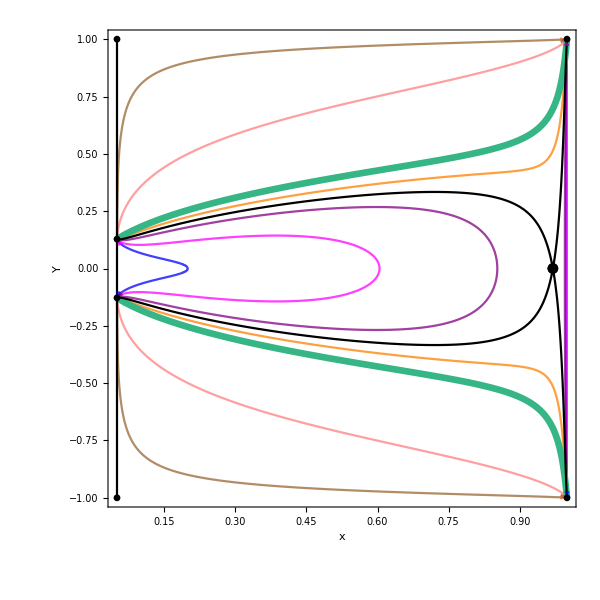

```mathematica
(*Show all components of plots*)
PhaseSpacec1=Show[Trajc1, FFSc1,CFSc1,Einsteinc1,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xOneEinsteinPointc1,0.2][[1]]
```

-3.56314

```mathematica
(*Plot the potential for this case*)
Uc1=Plot[{U[x,0.2][[1]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
(*Plot the energy from each trajectory in the phase space*)
```

```mathematica
c1Energy[1]=Plot[{Energy[0.2,0][[1]]},{x,0.05,0.2},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c1Energy[2]=Plot[{Energy[0.2,0.12][[1]]},{x,0.05,0.6},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c1Energy[3]=Plot[{Energy[0.2,0.18][[1]]},{x,0.05,0.85},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c1Energy[4]=Plot[{Energy[0.2,0.225][[1]]},{x,0.1,0.45},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c1Energy[5]=Plot[{Energy[0.2,0.5][[1]]},{x,0.6,0.73},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[6]=Plot[{Energy[0.2,0.5][[1]]},{x,0.27,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c1Energy[7]=Plot[{Energy[0.2,0.9][[1]]},{x,0.05,0.12},AxesLabel->{"x","U"},PlotStyle->{Brown,Dashed,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c1Energy[8]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c1Energy[9]=Plot[{Energy[0.2,0][[1]]},{x,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[10]=Plot[{Energy[0.2,0.12][[1]]},{x,0.6,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c1Energy[11]=Plot[{Energy[0.2,0.18][[1]]},{x,0.85,1},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc1=Table[c1Energy[i],{i,1,11}];
```

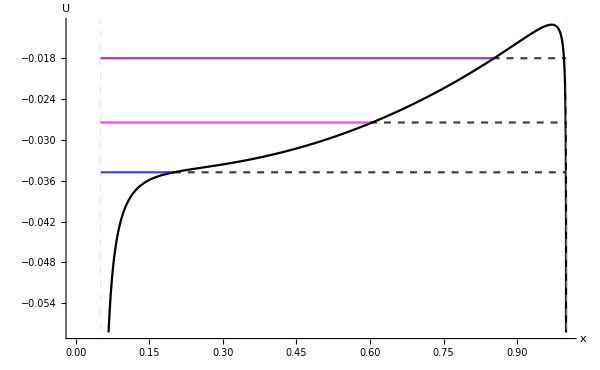

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc1=Show[Uc1,Energyc1,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

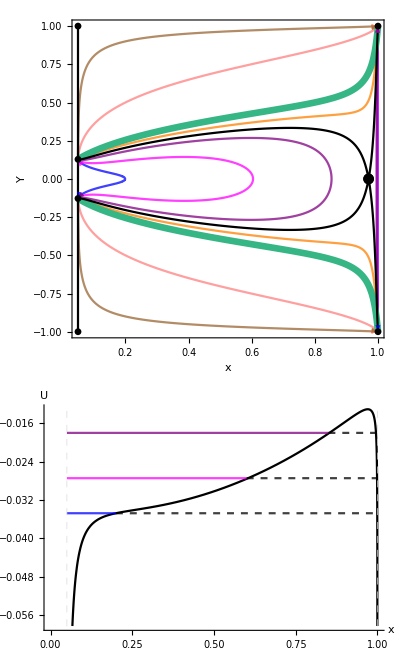

```mathematica
(*Plot the phase space and potential together*)
xYc1=GraphicsColumn[{PhaseSpacec1,Potentialc1},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc1.pdf",xYc1]*)
```

## Two Einstein Points: c2

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc2[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[2]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[2]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c2traj[1]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[2]=ContourPlot[Evaluate[trajc2[0,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[3]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0,0.6},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[4]=ContourPlot[Evaluate[trajc2[0.07,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[5]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[6]=ContourPlot[Evaluate[trajc2[0.09,0.1]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[7]=ContourPlot[Evaluate[trajc2[0.13,0.1]],{x,0,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[8]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[9]=ContourPlot[Evaluate[trajc2[0.4,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[10]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c2traj[11]=ContourPlot[Evaluate[trajc2[0.9,0.1]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc2=Table[c2traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc2=Plot[{FFS[[2]],-FFS[[2]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc2=Plot[{CFS[xTwoEinsteinPointsc2][[2]],-CFS[xTwoEinsteinPointsc2][[2]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc2=ListPlot[{{xTwoEinsteinPointsc2[[1]],0},{xTwoEinsteinPointsc2[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc2=ContourPlot[Accn[[2]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

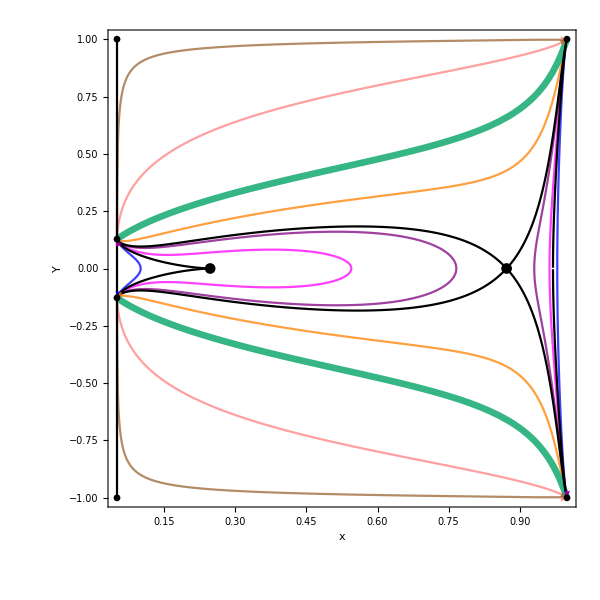

```mathematica
(*Show all components of plots*)
PhaseSpacec2=Show[Trajc2, FFSc2,CFSc2,Einsteinc2,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xTwoEinsteinPointsc2[[1]],0.1][[2]]
```

-5.33279×10^-9

```mathematica
d2Udx2[xTwoEinsteinPointsc2[[2]],0.1][[2]]
```

-0.180097

```mathematica
(*Plot the potential for this case*)
Uc2=Plot[{U[x,0.1][[2]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c2Energy[1]=Plot[{Energy[0.1,0][[2]]},{x,0.05,0.1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[2]=Plot[{Energy[0.1,0][[2]]},{x,0.98,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c2Energy[3]=Plot[{Energy[0.1,0.07][[2]]},{x,0.05,0.54},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[4]=Plot[{Energy[0.1,0.07][[2]]},{x,0.965,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c2Energy[5]=Plot[{Energy[0.1,0.09][[2]]},{x,0.05,0.765},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[6]=Plot[{Energy[0.1,0.09][[2]]},{x,0.93,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c2Energy[7]=Plot[{Energy[0.1,0.13][[2]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c2Energy[8]=Plot[{Energy[0.1,0.4][[2]]},{x,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c2Energy[9]=Plot[{Energy[0.1,0.9][[2]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c2Energy[10]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c2Energy[11]=Plot[{Energy[0.1,0][[2]]},{x,0.1,0.98},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[12]=Plot[{Energy[0.1,0.07][[2]]},{x,0.54,0.965},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c2Energy[13]=Plot[{Energy[0.1,0.09][[2]]},{x,0.765,0.93},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc2=Table[c2Energy[i],{i,1,13}];
```

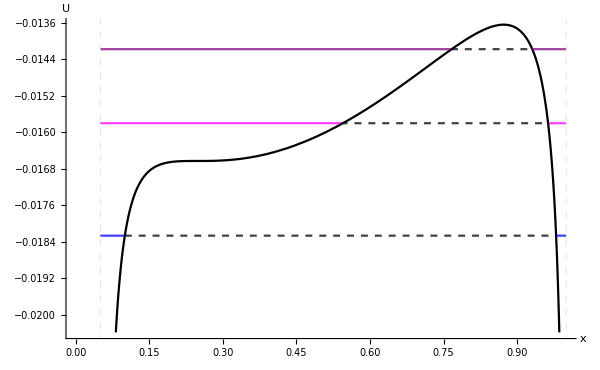

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc2=Show[Uc2,Energyc2,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

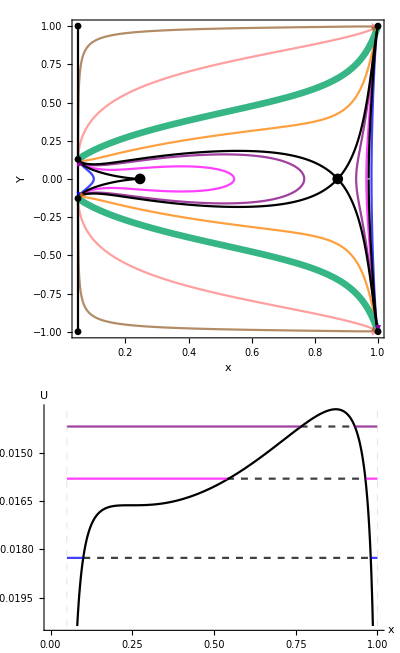

```mathematica
(*Plot the phase space and potential together*)
xYc2=GraphicsColumn[{PhaseSpacec2,Potentialc2},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc2.pdf",xYc2]*)
```

## Three Einstein Points: c3

```mathematica
(*This is the case where there is an extra bouncing regime*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc3[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[3]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[3]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c3traj[1]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[2]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.2,0.5},{Y,-1,1},PlotPoints->200,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[3]=ContourPlot[Evaluate[trajc3[0.071,0.08]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[4]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[5]=ContourPlot[Evaluate[trajc3[0.08,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[6]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0,0.8},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[7]=ContourPlot[Evaluate[trajc3[0.04,0.08]],{x,0.8,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[8]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[9]=ContourPlot[Evaluate[trajc3[0.12,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[10]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[11]=ContourPlot[Evaluate[trajc3[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[12]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c3traj[13]=ContourPlot[Evaluate[trajc3[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc3=Table[c3traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc3=Plot[{FFS[[3]],-FFS[[3]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc3=Plot[{CFS[xThreeEinsteinPointsc3][[3]],-CFS[xThreeEinsteinPointsc3][[3]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->600];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc3=ListPlot[{{xThreeEinsteinPointsc3[[1]],0},{xThreeEinsteinPointsc3[[2]],0},{xThreeEinsteinPointsc3[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc3=ContourPlot[Accn[[3]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

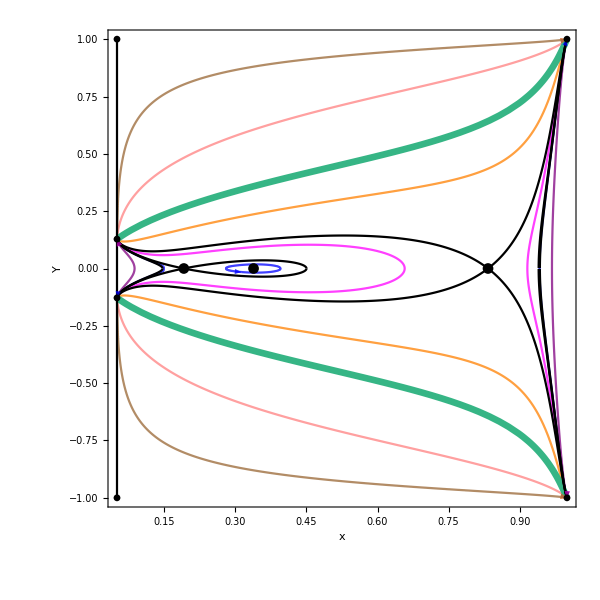

```mathematica
(*Show all components of plots*)
PhaseSpacec3=Show[Trajc3, FFSc3,CFSc3,Einsteinc3,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc3[[1]],0.155][[3]]
```

-0.134971

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[2]],0.155][[3]]
```

0.0402115

```mathematica
d2Udx2[xThreeEinsteinPointsc3[[3]],0.155][[3]]
```

-0.196611

```mathematica
(*Plot the potential for this case*)
Uc3=Plot[{U[x,0.08][[3]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed],PlotRange->{-0.016,-0.0105}];
```

```mathematica
c3Energy[1]=Plot[{Energy[0.08,0.071][[3]]},{x,0.05,0.15},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[2]=Plot[{Energy[0.08,0.071][[3]]},{x,0.275,0.4},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[3]=Plot[{Energy[0.08,0.071][[3]]},{x,0.94,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c3Energy[4]=Plot[{Energy[0.08,0.08][[3]]},{x,0.05,0.655},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[5]=Plot[{Energy[0.08,0.08][[3]]},{x,0.92,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c3Energy[6]=Plot[{Energy[0.08,0.04][[3]]},{x,0.05,0.09},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[7]=Plot[{Energy[0.08,0.04][[3]]},{x,0.97,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c3Energy[8]=Plot[{Energy[0.08,0.12][[3]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c3Energy[9]=Plot[{Energy[0.08,0.3][[3]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c3Energy[10]=Plot[{Energy[0.08,0.6][[3]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c3Energy[11]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c3Energy[12]=Plot[{Energy[0.08,0.071][[3]]},{x,0.15,0.275},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[13]=Plot[{Energy[0.08,0.071][[3]]},{x,0.4,0.94},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[14]=Plot[{Energy[0.08,0.08][[3]]},{x,0.655,0.92},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c3Energy[15]=Plot[{Energy[0.08,0.04][[3]]},{x,0.09,0.97},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc3=Table[c3Energy[i],{i,1,15}];
```

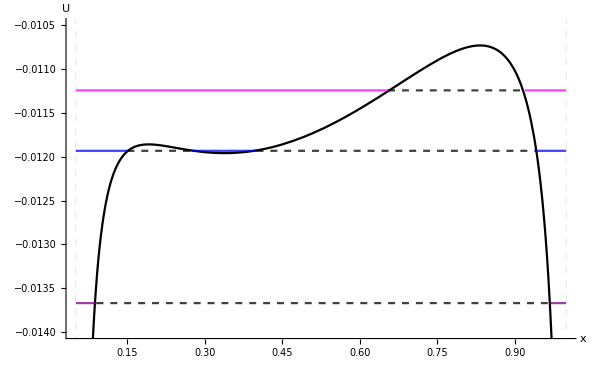

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc3=Show[Uc3,Energyc3,ImageSize->{600,400},BaseStyle->{FontSize->14},PlotRange->{-0.014,-0.0105}]
```

### Final Plot

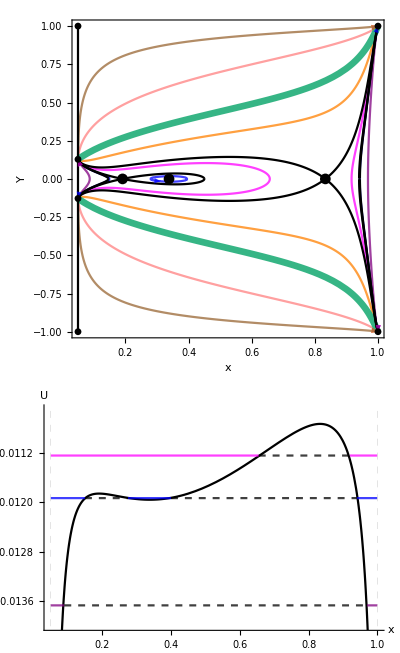

```mathematica
(*Plot the phase space and potential together*)
xYc3=GraphicsColumn[{PhaseSpacec3,Potentialc3},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc3.pdf",xYc3]*)
```

## Three Einstein Points: c4

```mathematica
(*This is the limiting 3 Einstein point case*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc4[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[4]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[4]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c4traj[1]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[2]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,0,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[3]=ContourPlot[Evaluate[trajc4[0.065,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[4]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0,0.3},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[5]=ContourPlot[Evaluate[trajc4[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[6]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[7]=ContourPlot[Evaluate[trajc4[0.11,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[8]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[9]=ContourPlot[Evaluate[trajc4[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[10]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c4traj[11]=ContourPlot[Evaluate[trajc4[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc4=Table[c4traj[i],{i,1,11}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc4=Plot[{FFS[[4]],-FFS[[4]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc4=Plot[{CFS[xThreeEinsteinPointsc4][[4]],-CFS[xThreeEinsteinPointsc4][[4]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc4=ListPlot[{{xThreeEinsteinPointsc4[[1]],0},{xThreeEinsteinPointsc4[[2]],0},{xThreeEinsteinPointsc4[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc4=ContourPlot[Accn[[4]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

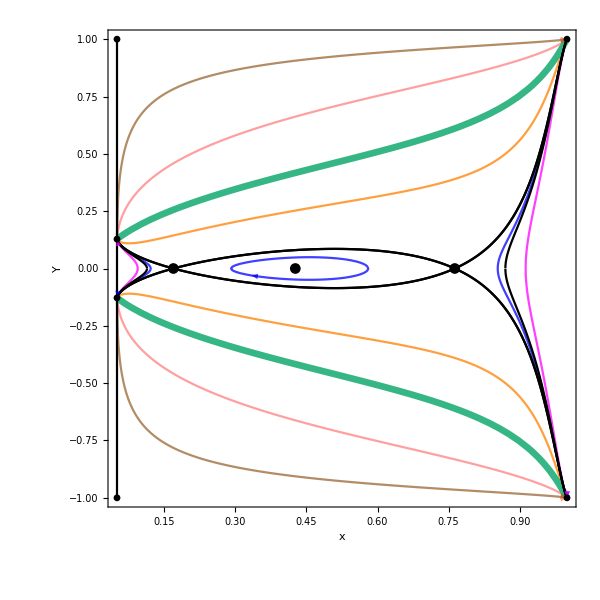

```mathematica
(*Show all components of plots*)
PhaseSpacec4=Show[Trajc4, FFSc4,CFSc4,Einsteinc4,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc4[[1]],0.08][[4]]
```

-0.110041

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[2]],0.08][[4]]
```

0.0143481

```mathematica
d2Udx2[xThreeEinsteinPointsc4[[3]],0.08][[4]]
```

-0.0357822

```mathematica
(*Plot the potential for this case*)
Uc4=Plot[{U[x,0.08][[4]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c4Energy[1]=Plot[{Energy[0.08,0.065][[4]]},{x,0.05,0.12},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[2]=Plot[{Energy[0.08,0.065][[4]]},{x,0.3,0.57},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[3]=Plot[{Energy[0.08,0.065][[4]]},{x,0.855,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c4Energy[4]=Plot[{Energy[0.08,0.05][[4]]},{x,0.05,0.095},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[5]=Plot[{Energy[0.08,0.05][[4]]},{x,0.91,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c4Energy[6]=Plot[{Energy[0.08,0.11][[4]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c4Energy[7]=Plot[{Energy[0.08,0.3][[4]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c4Energy[8]=Plot[{Energy[0.08,0.6][[4]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c4Energy[9]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c4Energy[10]=Plot[{Energy[0.08,0.065][[4]]},{x,0.12,0.3},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[11]=Plot[{Energy[0.08,0.065][[4]]},{x,0.57,0.855},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c4Energy[12]=Plot[{Energy[0.08,0.05][[4]]},{x,0.095,0.91},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc4=Table[c4Energy[i],{i,1,12}];
```

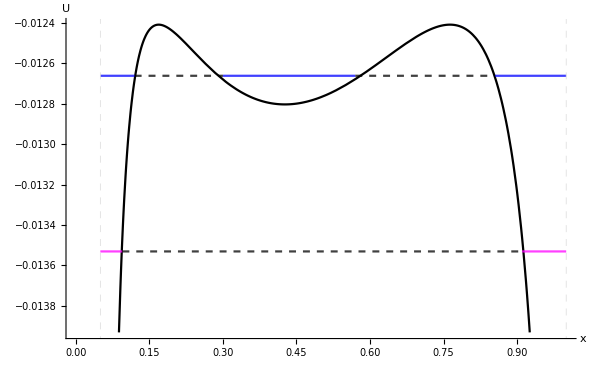

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc4=Show[Uc4,Energyc4,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

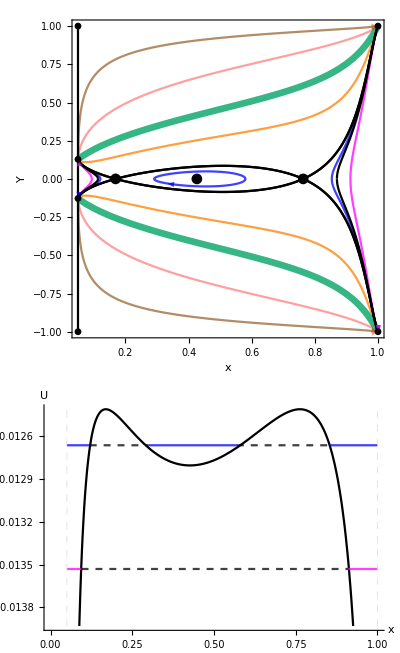

```mathematica
(*Plot the phase space and potential together*)
xYc4=GraphicsColumn[{PhaseSpacec4,Potentialc4},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc4.pdf",xYc4]*)
```

## Three Einstein Points: c5

```mathematica
(*The case with an extra turn-around region*)
```

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc5[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[5]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[5]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c5traj[1]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[2]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.2,0.7},{Y,-1,1},PlotPoints->150,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,0,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[3]=ContourPlot[Evaluate[trajc5[0.06,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[4]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[5]=ContourPlot[Evaluate[trajc5[0.065,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[6]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[7]=ContourPlot[Evaluate[trajc5[0.05,0.08]],{x,0.7,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[8]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[9]=ContourPlot[Evaluate[trajc5[0.11,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[10]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[11]=ContourPlot[Evaluate[trajc5[0.3,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[12]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c5traj[13]=ContourPlot[Evaluate[trajc5[0.6,0.08]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc5=Table[c5traj[i],{i,1,13}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc5=Plot[{FFS[[5]],-FFS[[5]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc5=Plot[{CFS[xThreeEinsteinPointsc5][[5]],-CFS[xThreeEinsteinPointsc5][[5]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->300];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc5=ListPlot[{{xThreeEinsteinPointsc5[[1]],0},{xThreeEinsteinPointsc5[[2]],0},{xThreeEinsteinPointsc5[[3]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc5=ContourPlot[Accn[[5]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

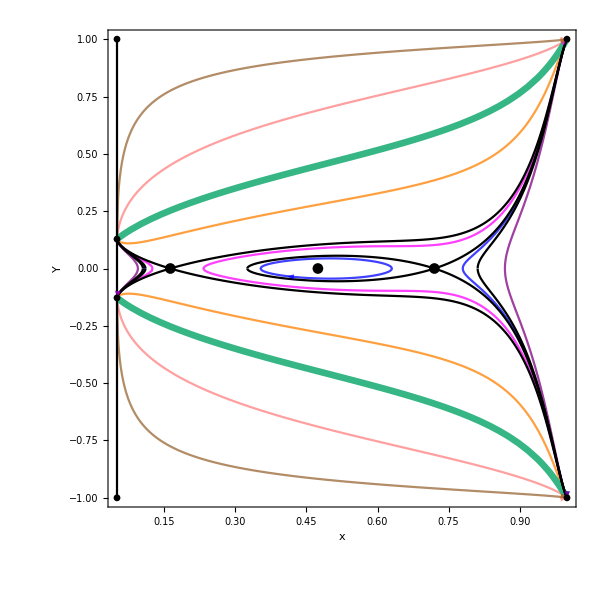

```mathematica
(*Show all components of plots*)
PhaseSpacec5=Show[Trajc5, FFSc5,CFSc5,Einsteinc5,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xThreeEinsteinPointsc5[[1]],0.08][[5]]
```

-0.136059

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[2]],0.08][[5]]
```

0.0116164

```mathematica
d2Udx2[xThreeEinsteinPointsc5[[3]],0.08][[5]]
```

-0.0219094

```mathematica
(*Plot the potential for this case*)
Uc5=Plot[{U[x,0.08][[5]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c5Energy[1]=Plot[{Energy[0.08,0.06][[5]]},{x,0.05,0.11},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[2]=Plot[{Energy[0.08,0.06][[5]]},{x,0.36,0.625},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[3]=Plot[{Energy[0.08,0.06][[5]]},{x,0.78,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c5Energy[4]=Plot[{Energy[0.08,0.065][[5]]},{x,0.235,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[5]=Plot[{Energy[0.08,0.065][[5]]},{x,0.05,0.125},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c5Energy[6]=Plot[{Energy[0.08,0.05][[5]]},{x,0.87,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[7]=Plot[{Energy[0.08,0.05][[5]]},{x,0.05,0.095},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c5Energy[8]=Plot[{Energy[0.08,0.11][[5]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c5Energy[9]=Plot[{Energy[0.08,0.3][[5]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c5Energy[10]=Plot[{Energy[0.08,0.6][[5]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c5Energy[11]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c5Energy[12]=Plot[{Energy[0.08,0.06][[5]]},{x,0.11,0.36},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[13]=Plot[{Energy[0.08,0.06][[5]]},{x,0.625,0.78},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[14]=Plot[{Energy[0.08,0.065][[5]]},{x,0.125,0.235},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c5Energy[15]=Plot[{Energy[0.08,0.05][[5]]},{x,0.095,0.87},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc5=Table[c5Energy[i],{i,1,15}];
```

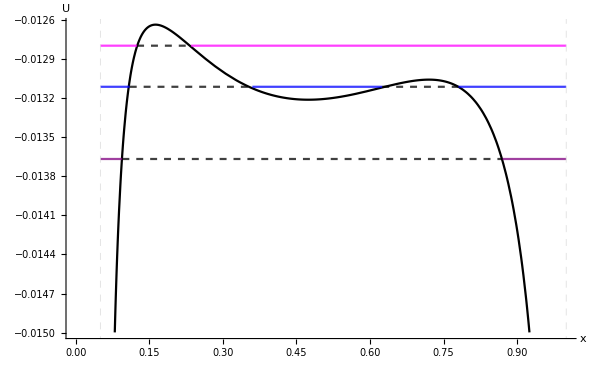

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc5=Show[Uc5,Energyc5,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

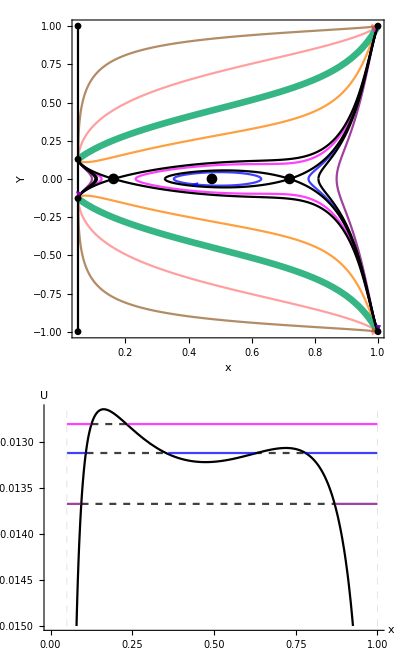

```mathematica
(*Plot the phase space and potential together*)
xYc5=GraphicsColumn[{PhaseSpacec5,Potentialc5},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc5.pdf",xYc5]*)
```

## Two Einstein Points: c6

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc6[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[6]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[6]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c6traj[1]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[2]=ContourPlot[Evaluate[trajc6[0,0.9]],{x,0.6,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue,Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[3]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[4]=ContourPlot[Evaluate[trajc6[0.4,0.9]],{x,0.3,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[5]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[6]=ContourPlot[Evaluate[trajc6[0.6,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[7]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[8]=ContourPlot[Evaluate[trajc6[0.9,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[9]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c6traj[10]=ContourPlot[Evaluate[trajc6[0.99,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc6=Table[c6traj[i],{i,1,10}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc6=Plot[{FFS[[6]],-FFS[[6]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS curves*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc6=Plot[{CFS[xTwoEinsteinPointsc6][[6]],-CFS[xTwoEinsteinPointsc6][[6]]},{x,0,1},PlotStyle->{Black},PlotRange->Full,PlotPoints->500];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc6=ListPlot[{{xTwoEinsteinPointsc6[[1]],0},{xTwoEinsteinPointsc6[[2]],0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc6=ContourPlot[Accn[[6]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

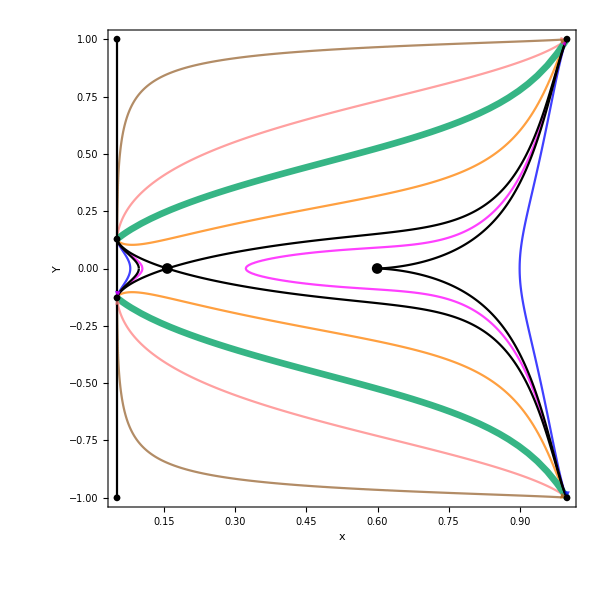

```mathematica
(*Show all components of plots*)
PhaseSpacec6=Show[Trajc6, FFSc6,CFSc6,Einsteinc6,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xTwoEinsteinPointsc6[[1]],0.9][[6]]
```

-8.33654

```mathematica
d2Udx2[xTwoEinsteinPointsc6[[2]],0.9][[6]]
```

-8.91109×10^-8

```mathematica
(*Plot the potential for this case*)
Uc6=Plot[{U[x,0.9][[6]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c6Energy[1]=Plot[{Energy[0.9,0][[6]]},{x,0.05,0.07},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[2]=Plot[{Energy[0.9,0][[6]]},{x,0.9,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c6Energy[3]=Plot[{Energy[0.9,0.4][[6]]},{x,0.05,0.105},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[4]=Plot[{Energy[0.9,0.4][[6]]},{x,0.322,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c6Energy[5]=Plot[{Energy[0.9,0.6][[6]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c6Energy[6]=Plot[{Energy[0.9,0.9][[6]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[7]=Plot[{Energy[0.9,0.99][[6]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c6Energy[8]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c6Energy[9]=Plot[{Energy[0.9,0][[6]]},{x,0.07,0.9},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c6Energy[10]=Plot[{Energy[0.9,0.4][[6]]},{x,0.105,0.322},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc6=Table[c6Energy[i],{i,1,10}];
```

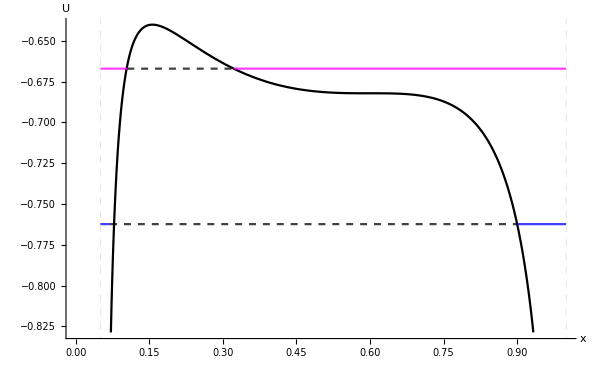

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc6=Show[Uc6,Energyc6,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

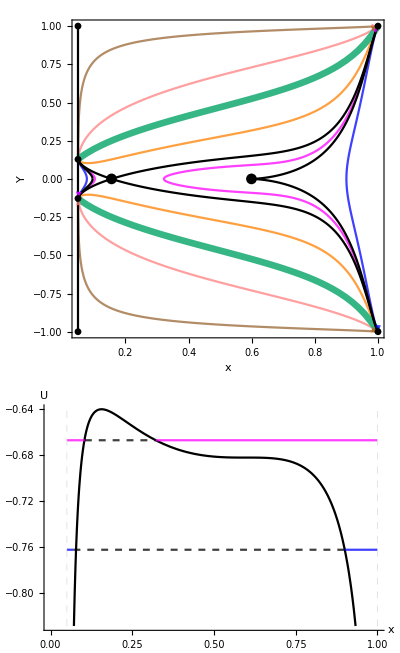

```mathematica
(*Plot the phase space and potential together*)
xYc6=GraphicsColumn[{PhaseSpacec6,Potentialc6},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc6.pdf",xYc6]*)
```

## One Einstein Point: c7

### Phase Space

```mathematica
(*Trajectories for the phase space*)
(*We plot the trajectories using the first integral (Friedmann equation) rather than the differential equations*)
trajc7[Y0_,x0_]:=Y^2/(1-Y^2)==x/3+z[x,c][[7]]/3+v[x,cv]/3-(1/a[x,x0]^2)*(x0/3+z[x0,c][[7]]/3+v[x0,cv]/3-Y0^2/(1-Y0^2));
```

```mathematica
(*Trajectories plotted individually to ensure arrows are pointing in the right direction*)
```

```mathematica
c7traj[1]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[2]=ContourPlot[Evaluate[trajc7[0,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[3]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[4]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[5]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0.2,1},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[6]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{x,0,0.2},{Y,-1,1},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[7]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[8]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[9]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[10]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[11]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,0,1},{Y,0,1},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[12]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{x,0,1},{Y,-1,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc7=Table[c7traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7=Plot[{FFS[[7]],-FFS[[7]]},{x,0,1},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}}];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7=Plot[{CFS[xOneEinsteinPointc7][[7]],-CFS[xOneEinsteinPointc7][[7]]},{x,0,1},PlotStyle->{Black}];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7=ListPlot[{{xOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc7=ContourPlot[Accn[[7]]==0,{x,0,1},{Y,-1,1},ContourStyle->{Red, Thick}];
```

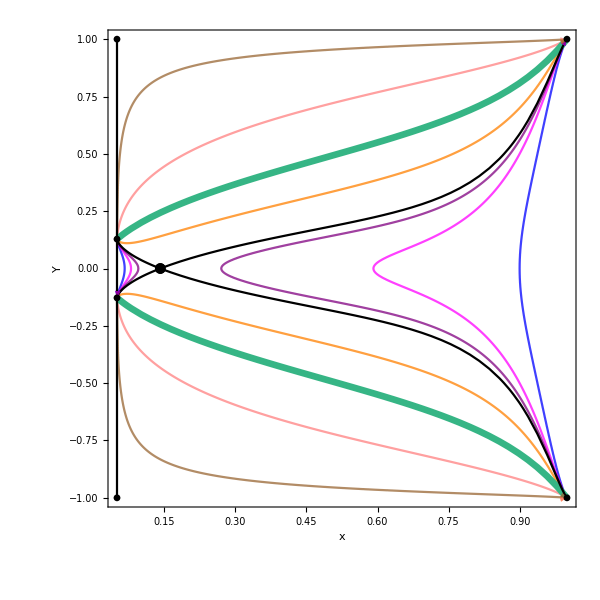

```mathematica
(*Show all components of plots*)
PhaseSpacec7=Show[Trajc7, FFSc7,CFSc7,Einsteinc7,Sep,FPShow,PlotRange->All,FrameLabel->{"x",Rotate["Y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

### Potential

```mathematica
(*Substitute Einstein points into the second derivative to find whether point is a maximum or a minimum*)
(*A positive/negative value means it's a minimum/maximum*)
d2Udx2[xOneEinsteinPointc7,0.9][[7]]
```

-13.8236

```mathematica
(*Plot the potential for this case*)
Uc7=Plot[{U[x,0.9][[7]]},{x,0,1},AxesLabel->{"x","U"},PlotStyle->{Black},GridLines->{{.05,1},{}},GridLinesStyle->Directive[Thick,Dashed]];
```

```mathematica
c7Energy[1]=Plot[{Energy[0.9,0][[7]]},{x,0.9,1},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[2]=Plot[{Energy[0.9,0][[7]]},{x,0.05,0.06},AxesLabel->{"x","U"},PlotStyle->{Blue,Opacity[0.75]}];
```

```mathematica
c7Energy[3]=Plot[{Energy[0.9,0.5][[7]]},{x,0.6,1},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[4]=Plot[{Energy[0.9,0.5][[7]]},{x,0.05,0.08},AxesLabel->{"x","U"},PlotStyle->{Magenta,Opacity[0.75]}];
```

```mathematica
c7Energy[5]=Plot[{Energy[0.9,0.56][[7]]},{x,0.275,1},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[6]=Plot[{Energy[0.9,0.56][[7]]},{x,0.05,0.099},AxesLabel->{"x","U"},PlotStyle->{Purple,Opacity[0.75]}];
```

```mathematica
c7Energy[7]=Plot[{Energy[0.9,0.7][[7]]},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{Orange,Opacity[0.75]}];
```

```mathematica
c7Energy[8]=Plot[{Energy[0.9,0.92][[7]]},{x,0.2,1},AxesLabel->{"x","U"},PlotStyle->{Pink,Opacity[0.75]}];
```

```mathematica
c7Energy[9]=Plot[{Energy[0.9,0.99][[7]]},{x,0.6,1},AxesLabel->{"x","U"},PlotStyle->{Brown,Opacity[0.75]}];
```

```mathematica
(*Energy of a trajectory that follows the FFS*)
c7Energy[10]=Plot[{0},{x,0.05,1},AxesLabel->{"x","U"},PlotStyle->{RGBColor[0.21,0.71,0.52],Thickness[0.008]}];
```

```mathematica
(*Plot dashed black lines between trajectories of the same energy*)
```

```mathematica
c7Energy[11]=Plot[{Energy[0.9,0][[7]]},{x,0.06,0.9},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[12]=Plot[{Energy[0.9,0.5][[7]]},{x,0.08,0.6},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
c7Energy[13]=Plot[{Energy[0.9,0.56][[7]]},{x,0.099,0.275},AxesLabel->{"x","U"},PlotStyle->{Black,Dashed,Opacity[0.75]}];
```

```mathematica
(*Add energies into a table*)
Energyc7=Table[c7Energy[i],{i,1,13}];
```

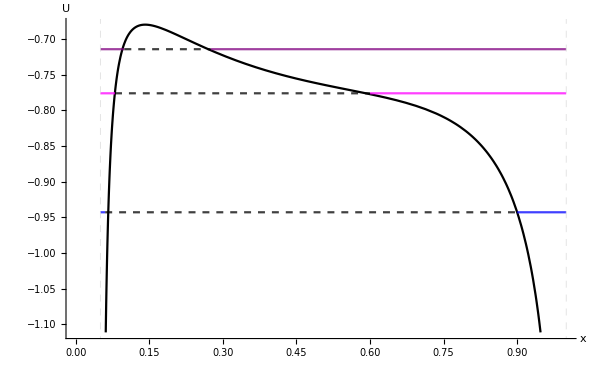

```mathematica
(*Show the potential and energy of the trajectories together*)
Potentialc7=Show[Uc7,Energyc7,ImageSize->{600,400},BaseStyle->{FontSize->14}]
```

### Final Plot

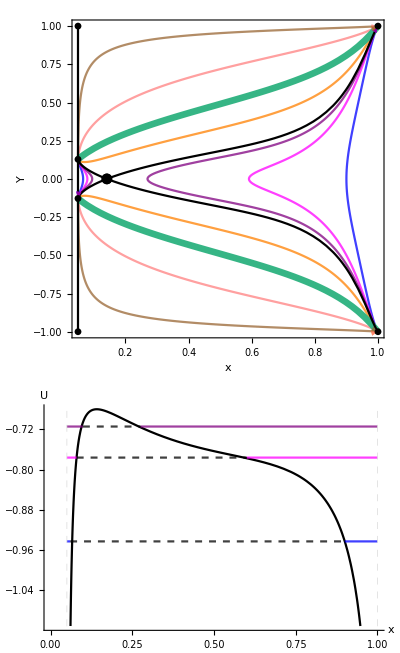

```mathematica
(*Plot the phase space and potential together*)
xYc7=GraphicsColumn[{PhaseSpacec7,Potentialc7},Spacings->{0,-20}]
```

```mathematica
(*Export["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\Figures\\xY_Plots\\xYc7.pdf",xYc7]*)
```